```mathematica
"Light Field Fourier Transform"
```

```mathematica
Γ := EulerGamma
1/(√(2*π))*∫_(-∞)^∞ (Exp[-(4*Log[2])/Γ^2*(t-t0)^2]*Cos[w*(t-t0)+ϕ])*Exp[ⅈ*ω*t]ⅆt
FourierTransform[(Exp[-(4*Log[2])/Γ^2*(t-t0)^2]*Cos[w*(t-t0)+ϕ]),t,ω]
1/(√(2*π))*∫_(-∞)^∞ (Cos[w*(t-t0)+ϕ])*Exp[ⅈ*ω*t]ⅆt
FourierTransform[Cos[w*(t-t0)+ϕ],t,ω]
```

(ⅇ^(-ⅈ ϕ+ⅈ t0 ω-(EulerGamma^2 (w+ω)^2)/(16 Log[2])) (ⅇ^(2 ⅈ ϕ)+ⅇ^((EulerGamma^2 w ω)/Log[16])) EulerGamma)/(4 √(2 Log[2]))

1/4 EulerGamma (Cos[ϕ-t0 ω]-ⅈ Sin[ϕ-t0 ω]) (Cosh[(EulerGamma^2 (w-ω)^2)/(16 Log[2])]/(√Log[4])+(2 Cos[2 ϕ+(ⅈ EulerGamma^2 (w+ω)^2)/(16 Log[2])])/(√Log[256])+(2 ⅈ Sin[2 ϕ+(ⅈ EulerGamma^2 (w+ω)^2)/(16 Log[2])])/(√Log[256])-Sinh[(EulerGamma^2 (w-ω)^2)/(16 Log[2])]/(√Log[4]))

```mathematica
RTlightpulse[t_, w_, Γ_, t0_, E0_, ϕ_]:=Exp[-(4*Log[2])/Γ^2*(t-t0)^2]*Cos[w*(t-t0)+ϕ]
LRlightpulse[ω_,  w_, Γ_, t0_, E0_, ϕ_]:=1/4* Γ*(Cos[t0*ω -ϕ]-ⅈ Sin[t0*ω-ϕ])(Cosh[(Γ^2 (w-ω)^2)/(16 Log[2])]/(√Log[4])+(2 Cos[2 ϕ+(ⅈ* Γ^2* (w+ω)^2)/(16 Log[2])])/(√Log[256])+(2 ⅈ Sin[2 ϕ+(ⅈ* Γ^2*(w+ω)^2)/(16 Log[2])])/(√Log[256])-Sinh[(Γ^2 (w-ω)^2)/(16 Log[2])]/(√Log[4]))
```

```mathematica
"Example Light-Field 1"
```

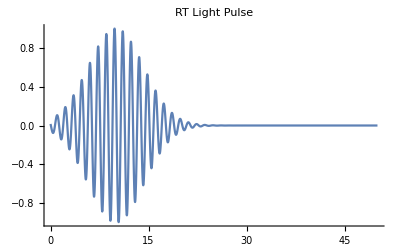

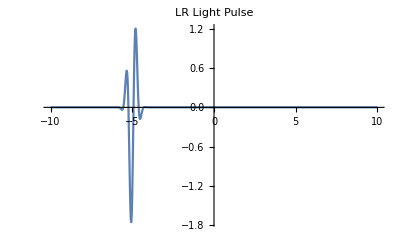

-Graphics-

```mathematica
ww    := 5
ΓΓ   := 10
t0   := 10
Eu0 := 0.01
ϕu    := 3.141592/3
Plot[Re[RTlightpulse[t, ww, ΓΓ, t0, Eu0, ϕu]], {t, 0, 50}, PlotRange->All,PlotLabel->"RT Light Pulse" ]
Plot[Re[LRlightpulse[ω, ww, ΓΓ, t0, Eu0, ϕu]], {ω, -10, 10}, PlotRange->All,PlotLabel->"LR Light Pulse" ]
```